```mathematica
Clear[r, K, cmax, Ef, q, C0]
```

# Functional responses & the Scheffer Model

## Using Mangel’s suggested functional response

```mathematica
(cmax Ef N q)/(Ef N q+0.2)
```

### Finding Equilibria

```mathematica
dN = r N (1 - N/K) - cmax Ef N q/ (Ef N q + C0)
```

```mathematica
Solve[dN==0,N]
```

{{N→0},{N→(-C0 r+Ef K q r-√(4 Ef q r (-cmax Ef K q+C0 K r)+(-C0 r+Ef K q r)^2))/(2 Ef q r)},{N→(-C0 r+Ef K q r+√(4 Ef q r (-cmax Ef K q+C0 K r)+(-C0 r+Ef K q r)^2))/(2 Ef q r)}}

### When are the equilbria biologically meaningful (greater than zero, real?)

```mathematica
r = 10
C0 = 2
cmax = 5
K = 100
q = .2
```

10

2

5

100

0.2

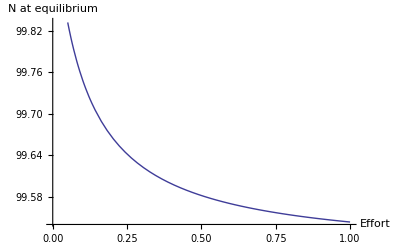

```mathematica
Plot[(-C0 r+Ef K q r+√(4 Ef q r (-cmax Ef K q+C0 K r)+(-C0 r+Ef K q r)^2))/(2 Ef q r),{Ef,0,1},AxesLabel -> {"Effort", "N at equilibrium"}]
```

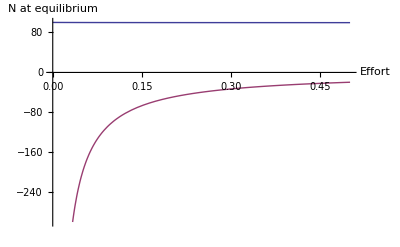

```mathematica
Plot[{(-C0 r+Ef K q r+√(4 Ef q r (-cmax Ef K q+C0 K r)+(-C0 r+Ef K q r)^2))/(2 Ef q r),(-C0 r+Ef K q r-√(4 Ef q r (-cmax Ef K q+C0 K r)+(-C0 r+Ef K q r)^2))/(2 Ef q r)},{Ef,0,.5},AxesLabel -> {"Effort", "N at equilibrium"}]
```

### Plotting Effort versus Yield

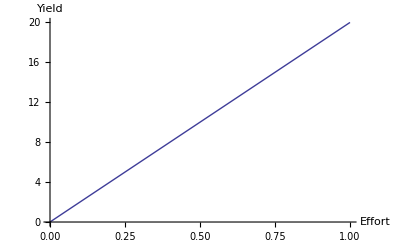

```mathematica
Plot[ q*Ef*(-C0 r+Ef K q r+√(4 Ef q r (-cmax Ef K q+C0 K r)+(-C0 r+Ef K q r)^2))/(2 Ef q r),{Ef,0,1},AxesLabel->{Effort,Yield}]
```

### As compared to the Scheffer Model for the same parameters

```mathematica
Clear[r, K, q]
```

```mathematica
dN = r N (1 - N/K)-q Ef N
```

#### Equilibrium values

```mathematica
FullSimplify[Solve[dN==0,N]]
```

{{N→0},{N→K-(Ef K q)/r}}

#### Equilibrium Yield

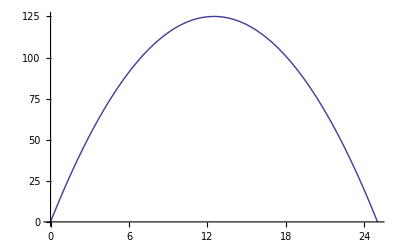

```mathematica
Plot[q*Ef*(K-(Ef K q)/r),{Ef,0,25}]
```

Which is a parabola. So can be maximized.

## Using Functional responses from Fryxell et al. (2004)

### Pred (fisher) grouping

```mathematica
dN = r N (1 - N/K) - a N /(G + a(G h1 + h2)N)
```

### Equilibrium values

```mathematica
FullSimplify[Solve[dN==0,N]]
```

{{N→0},{N→(-√(r (r (a K (G h1+h2)+G)^2-4 a^2 K (G h1+h2)))+G r (a h1 K-1)+a h2 K r)/(2 a r (G h1+h2))},{N→(√(r (r (a K (G h1+h2)+G)^2-4 a^2 K (G h1+h2)))+G r (a h1 K-1)+a h2 K r)/(2 a r (G h1+h2))}}

### Plot yield equation, varying E

```mathematica
G = 10
r = 5
K = 100
q = .2
a = 2
h1 = .5
h2 = .5
```

10

5

100

0.2

2

0.5

0.5

```mathematica
Plot[(√(r (r (a K (G h1+h2)+G)^2-4 a^2 K (G h1+h2)))+G r (a h1 K-1)+a h2 K r)/(2 a r (G h1+h2)),
```

Ah, but the problem is, what is effor here. This brings me to the discussion of how to convert their functional response into effort.